More SVD - working with tolerence

```mathematica
data={{1.02,.39},{.95,.32},{.87,.27},{.77,.22},{.67,.18},{.56,.15},{.44,.13},{.30,.12},{.16,.13},{.01,.15}}
```

{{1.02,0.39},{0.95,0.32},{0.87,0.27},{0.77,0.22},{0.67,0.18},{0.56,0.15},{0.44,0.13},{0.3,0.12},{0.16,0.13},{0.01,0.15}}

```mathematica
aa={#[[2]]^2,#[[2]]*#[[1]],#[[1]],#[[2]],1} &/@data
b=#[[1]]^2 & /@data
```

{{0.1521,0.3978,1.02,0.39,1},{0.1024,0.304,0.95,0.32,1},{0.0729,0.2349,0.87,0.27,1},{0.0484,0.1694,0.77,0.22,1},{0.0324,0.1206,0.67,0.18,1},{0.0225,0.084,0.56,0.15,1},{0.0169,0.0572,0.44,0.13,1},{0.0144,0.036,0.3,0.12,1},{0.0169,0.0208,0.16,0.13,1},{0.0225,0.0015,0.01,0.15,1}}

{1.0404,0.9025,0.7569,0.5929,0.4489,0.3136,0.1936,0.09,0.0256,0.0001}

```mathematica
LeastSquares[aa,b]
```

{-2.63563,0.143646,0.551447,3.22294,-0.432894}

```mathematica
plotellipse[{a_,b_,c_,d_,e_},wind_]:=ContourPlot[a*y^2+b*x*y+c*x+d*y+e==x^2,{x,-wind,wind},{y,-wind,wind}]
```

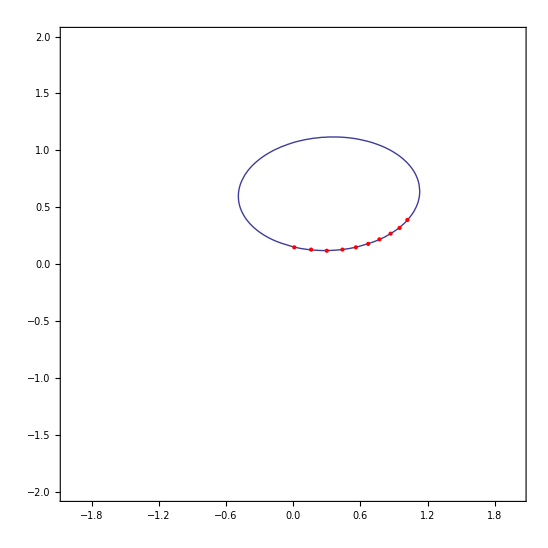

```mathematica
Show[{plotellipse[LeastSquares[aa,b],2],ListPlot[data,PlotStyle->Red]}]
```

{{1.01726,0.387313},{0.951087,0.323123},{0.867557,0.27337},{0.769991,0.22003},{0.671162,0.177864},{0.564754,0.147025},{0.444829,0.129272},{0.304983,0.116733},{0.162699,0.126748},{0.011026,0.147153}}

{{0.150011,0.393997,1.01726,0.387313,1},{0.104409,0.307319,0.951087,0.323123,1},{0.0747314,0.237165,0.867557,0.27337,1},{0.0484131,0.169421,0.769991,0.22003,1},{0.0316358,0.119376,0.671162,0.177864,1},{0.0216164,0.083033,0.564754,0.147025,1},{0.0167111,0.0575037,0.444829,0.129272,1},{0.0136267,0.0356018,0.304983,0.116733,1},{0.0160649,0.0206217,0.162699,0.126748,1},{0.021654,0.0016225,0.011026,0.147153,1}}

{1.03482,0.904567,0.752656,0.592886,0.450458,0.318947,0.197873,0.0930149,0.0264709,0.000121572}

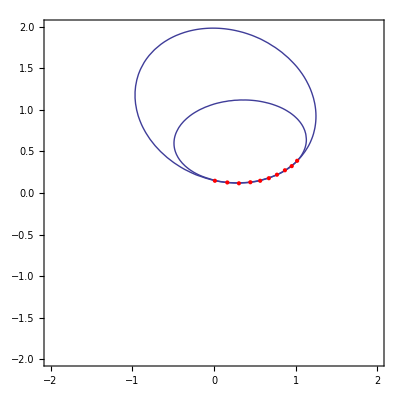

```mathematica
data2=data+RandomReal[{-.005,.005},{10,2}]
aa2={#[[2]]^2,#[[2]]*#[[1]],#[[1]],#[[2]],1} &/@data2
b2=#[[1]]^2 & /@data2
Show[{plotellipse[LeastSquares[aa,b],2],plotellipse[LeastSquares[aa2,b2],2]},ListPlot[data2,PlotStyle->Red]]
```

```mathematica
{u,w,v}=SingularValueDecomposition[aa];
w // MatrixForm
Diagonal[w][[1]]/Diagonal[w][[-1]]
```

(3.78604 | 0. | 0. | 0. | 0.
0. | 0.944923 | 0. | 0. | 0.
0. | 0. | 0.208913 | 0. | 0.
0. | 0. | 0. | 0.0230432 | 0.
0. | 0. | 0. | 0. | 0.00549953
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

688.429

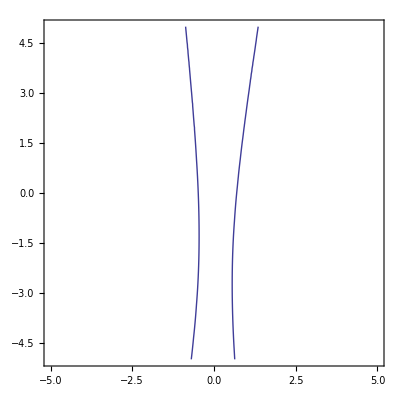
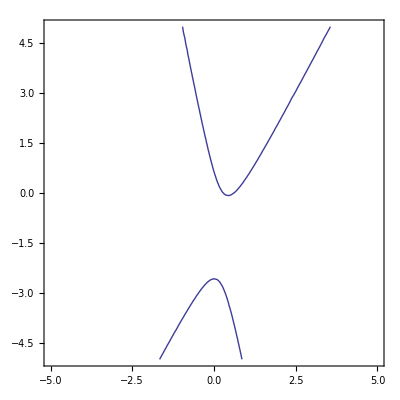
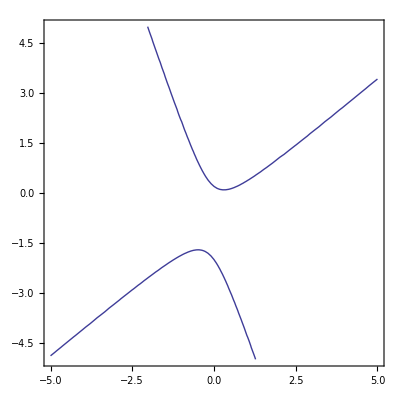
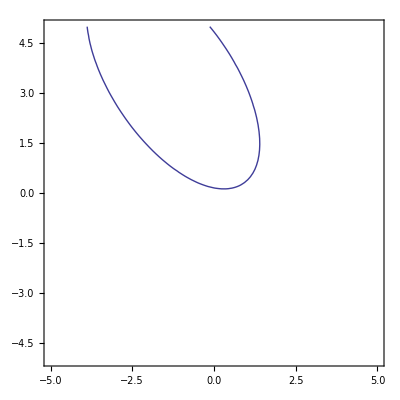
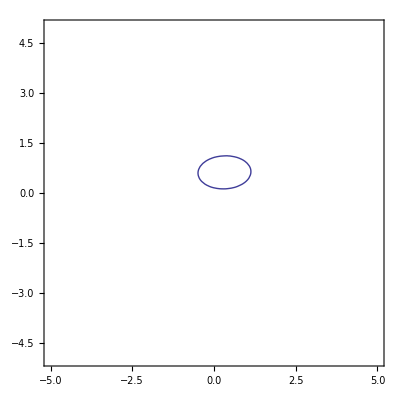

```mathematica
Do[{uu[i],ww[i],vv[i]}=SingularValueDecomposition[aa,i];
aaa[i]=uu[i].ww[i].Transpose[vv[i]],
{i,1,5}]
Table[plotellipse[LeastSquares[aaa[i],b],5],{i,1,5}]
```

{{1.02089,0.393004},{0.948415,0.31525},{0.874727,0.274626},{0.774362,0.215967},{0.665341,0.17506},{0.555742,0.148103},{0.443403,0.127642},{0.295563,0.117267},{0.159647,0.126962},{0.00907505,0.151726}}

{{0.154452,0.401212,1.02089,0.393004,1},{0.0993826,0.298988,0.948415,0.31525,1},{0.0754194,0.240223,0.874727,0.274626,1},{0.0466418,0.167237,0.774362,0.215967,1},{0.0306459,0.116475,0.665341,0.17506,1},{0.0219344,0.0823068,0.555742,0.148103,1},{0.0162925,0.0565968,0.443403,0.127642,1},{0.0137514,0.0346596,0.295563,0.117267,1},{0.0161195,0.0202691,0.159647,0.126962,1},{0.0230207,0.00137692,0.00907505,0.151726,1}}

{1.04221,0.89949,0.765147,0.599636,0.442679,0.308849,0.196606,0.0873574,0.025487,0.0000823565}

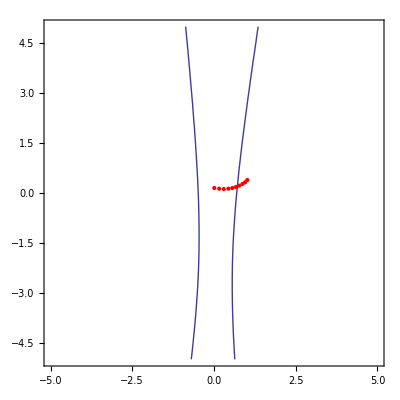
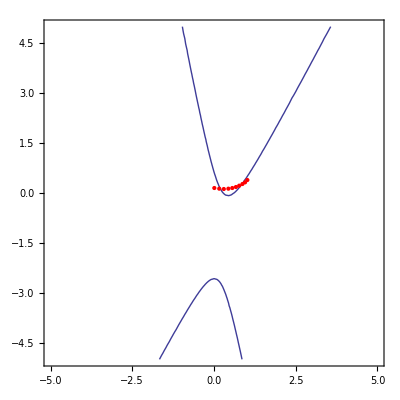
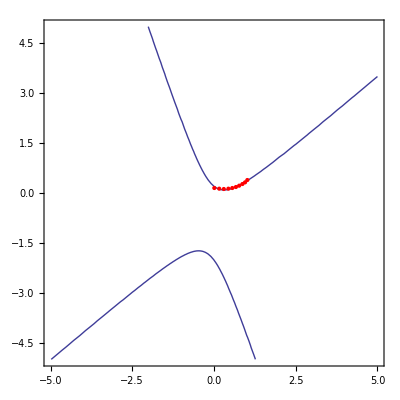
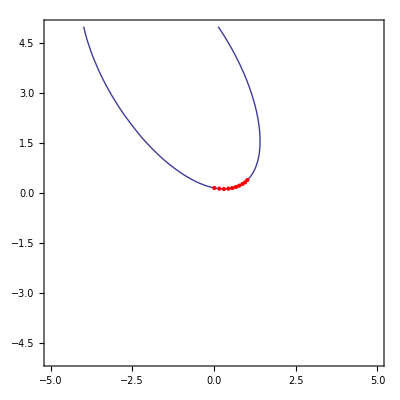
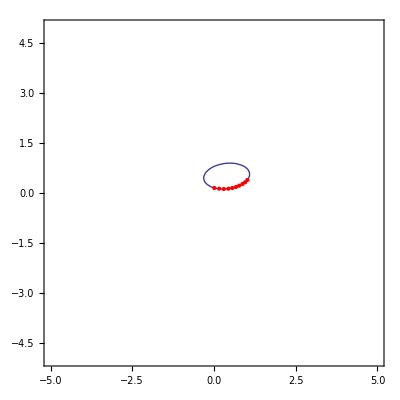

```mathematica
data2=data+RandomReal[{-.005,.005},{10,2}]
aa2={#[[2]]^2,#[[2]]*#[[1]],#[[1]],#[[2]],1} &/@data2
b2=#[[1]]^2 & /@data2
Do[{uu[i],ww[i],vv[i]}=SingularValueDecomposition[aa2,i];
aaa[i]=uu[i].ww[i].Transpose[vv[i]],
{i,1,5}]
Table[Show[{plotellipse[LeastSquares[aaa[i],b2],5],ListPlot[data,PlotStyle->Red]}],{i,1,5}]
```

```mathematica
data=Import["http://www.dougstats.com/13-14RD.Team.txt","Lines"];
temp=data[[2;;]] //StringSplit //ToExpression; (* get rid of header, split by spaces, toExp *)
(*stats={#[[2]]/(#[[3]]+#[[2]]),#[[5]]/#[[6]],#[[7]]/#[[8]],#[[9]]/#[[10]],#[[12]],#[[18]],#[[15]]}& /@temp //N;*)
stats={#[[2]]/(#[[3]]+#[[2]]),#[[5]]/#[[6]],#[[7]]/#[[8]],#[[9]]/#[[10]],#[[12]],#[[18]],#[[15]]}& /@temp //N;
```

```mathematica
{u,w,v}=SingularValueDecomposition[stats];
w//MatrixForm
```

(38217.3 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 798.143 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 341.406 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.743875 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.258122 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0859381 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0647403
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.)

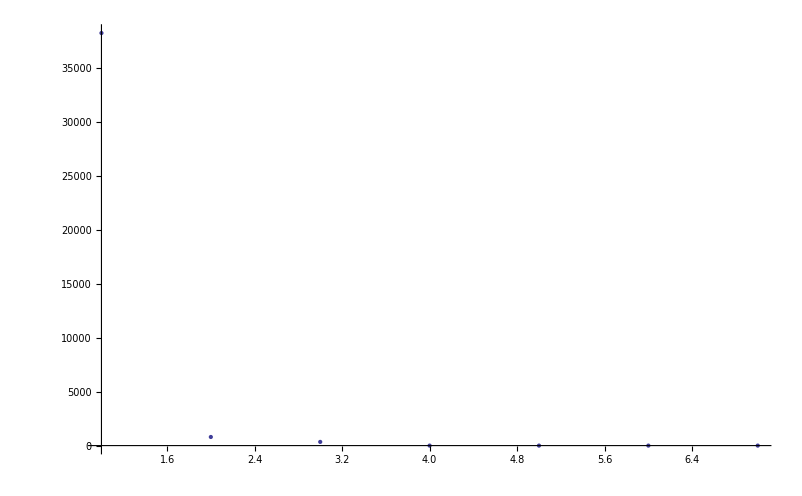

```mathematica
ListPlot[Diagonal[w],PlotRange->All]
```

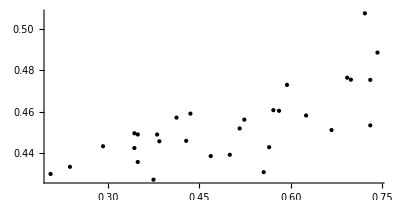

```mathematica
Graphics[Tooltip[Point[#[[2]]],#[[1]]]& /@Transpose[{temp[[All,1]],u.w.Transpose[v[[1;;2]]]}],Axes->True, AspectRatio->.5]
```

```mathematica
Graphics3D[Tooltip[Point[#[[2]]],#[[1]]]& /@Transpose[{temp[[All,1]],u.w.Transpose[v[[1;;3]]]}],Axes->True]
```

-Graphics3D-